## Введение во временные ряды

### Литература

1. Rob J Hyndman, George Athanasopoulos. Forecasting: Principles and Practice: https://otexts.com/fpp2/
2. G. E. P. Box, D. R. Cox. An analysis of transformations, Journal of the Royal Statistical Society, Series B, 26, 211-252 (1964)

## 1. Постановка задачи прогнозирования

### 1.1. Понятия временного ряда и прогнозирования

Временной ряд – последовательность значений признака y, измеряемого через постоянные временные интервалы:

y_1,y_2,...,y_T, y_t∈ℝ.

Примерами временных рядов могут выступать ряды среднедневных цен на акции определенной компании, рыночные цены, объемы продаж в торговых сетях, объемы потребления и цены электроэнергии, дорожный трафик и т. д. Ещё один пример временного ряда представлен на рисунке – это объемы перевозок интернациональных авиакомпаний с января 1949 г. до декабря 1960 г. в тысячах человек.

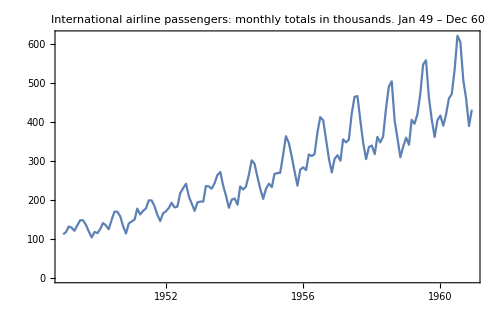

```mathematica
passengers=ExampleData[{"Statistics","InternationalAirlinePassengers"},"TimeSeries"];
DateListPlot[passengers,Joined->True,ImageSize->500,PlotLabel->"International airline passengers: monthly totals in thousands. Jan 49 – Dec 60"]
```

Задача прогнозирования состоит в нахождении функции f_T:

y_(T+h)≈f_T(y_T,...,y_1,h)≡(ŷ)_(T+h|T),

где h∈{1,2,...,H}, H – горизонт прогнозирования.

Предсказательный интервал – интервал, в котором предсказываемая величина окажется с вероятностью не меньше заданной.

### 1.2. Модель регрессии

Можно свести задачу прогнозирования к задаче обучения с учителем. Процесс разворачивается во времени, поэтому будем строить модель зависимости целевого признака от времени. Регрессия может быть линейной, квадратичной или даже показательной.

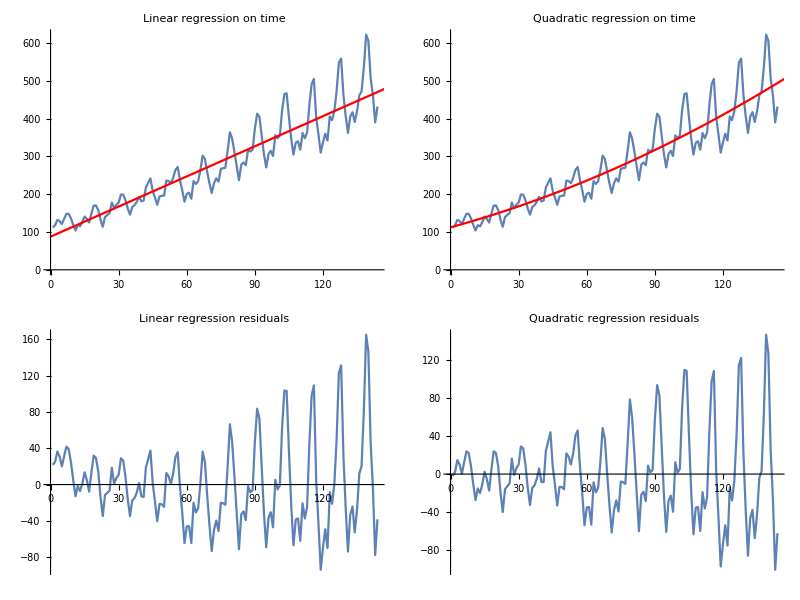

```mathematica
lplt=ListLinePlot[Normal[passengers]⟦All,2⟧,Axes->{False,True}];
line=Fit[Normal[passengers]⟦All,2⟧, {1,x},x];
linpred=(line/.x->#)&/@Range[Length@Normal@passengers];
quadpred=(parabola/.x->#)&/@Range[Length@Normal@passengers];
parabola=Fit[Normal[passengers]⟦All,2⟧, {1,x,x^2}, x];
Grid[{
{Show[lplt,Plot[line,{x,0,160},PlotStyle->Red,Axes->{False,True}],
ImageSize->300,AspectRatio->3/4,PlotLabel->"Linear regression on time"],Show[lplt,Plot[parabola,{x,0,160},PlotStyle->Red,Axes->{False,True}],
ImageSize->300,AspectRatio->3/4,PlotLabel->"Quadratic regression on time"]},
{ListLinePlot[Normal[passengers]⟦All,2⟧-linpred,Axes->{False,True},ImageSize->300,AspectRatio->3/4,PlotLabel->"Linear regression residuals"],
ListLinePlot[Normal[passengers]⟦All,2⟧-quadpred,Axes->{False,True},ImageSize->300,AspectRatio->3/4,PlotLabel->"Quadratic regression residuals"]}},
Spacings->{5,2}]
```

Остатки таких моделей не похожи на случайный шум, в них остается большая часть информации, которая не была учтена. Вид остатков показывает, что можно построить более сложную модель, которая будет лучше описывать имеющиеся данные, а также давать более точные прогнозы в будущем.

### 1.3. Компоненты временных рядов

Поведение временных рядов можно описать следующими характеристиками:
	•  тренд – плавное долгосрочное изменение уровня ряда;
	•  сезонность – циклические изменения уровня ряда с постоянным периодом;
	•  цикл – изменения уровня ряда с переменным периодом (экономические циклы, периоды солнечной активности);
	•  ошибка – непрогнозируемая случайная компонента ряда;
	•  разладка – смена модели ряда.

Рассмотрим данные продаж шампуня по месяцам. На графике виден повышающийся тренд, который можно описать линейной или квадратичной функцией. Сложно выделить на этом участке в данных циклы или сезонность.

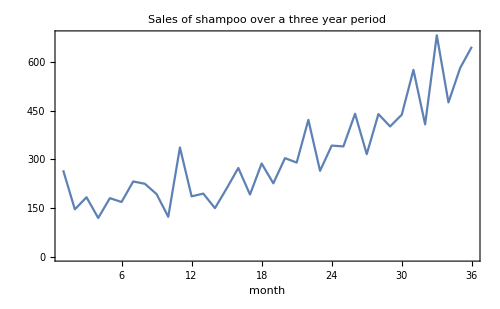

```mathematica
SetDirectory[NotebookDirectory[]];
shampoo=Import["sales-of-shampoo-over-a-three-ye.csv"];
ListLinePlot[shampoo⟦2;;-4,2⟧,PlotLabel->"Sales of shampoo over a three year period",AxesLabel->{"month",None},ImageSize->500,Frame->True,PlotRange->All]
```

Теперь рассмотрим данные за несколько лет о суммарном объеме электричества, произведенного за месяц в Австралии. На графике, как и в предыдущем случае, виден повышающийся тренд. Кроме того, наблюдается годовая сезонность: значение признака совершает колебания, минимум которых всегда приходится на зиму, а максимум – на середину лета. Это легко объяснить тем, что зимой электричества необходимо меньше всего, это самый теплый сезон в Австралии.

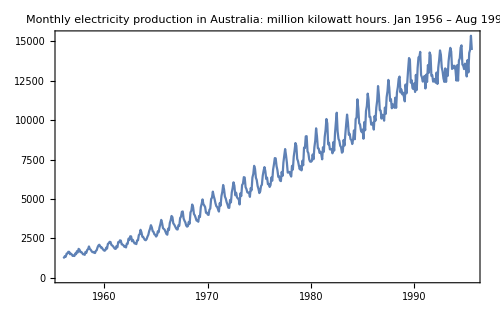

```mathematica
electricity=Import["monthly-electricity-production-i.csv"];
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@electricity⟦2;;-4⟧,PlotLabel->"Monthly electricity production in Australia: million kilowatt hours. Jan 1956 – Aug 1995",ImageSize->500]
```

Следующий пример – объем проданной жилой недвижимости в США за месяц (рис. 1.6). На графике наблюдается сочетание двух основных компонент. Первая компонента – это годовая сезонность (минимум всегда приходится на зиму, а максимум – на середину лета), а вторая – это циклы, связанные с изменением среднего уровня экономической активности (период в данном случае составляет 7-9 лет).

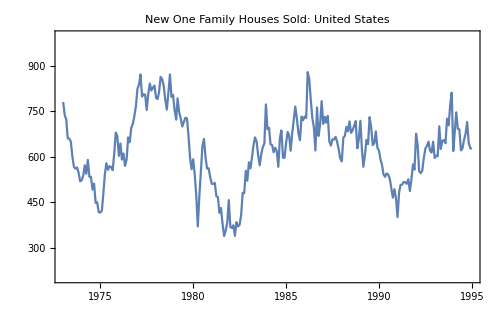

```mathematica
hsales=Import["HSN1F.csv"];
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@hsales⟦2;;⟧,PlotLabel->"New One Family Houses Sold: United States",ImageSize->500,PlotRange->{All,{200,1000}}]
```

## 2. Автокорреляция

### 2.1. Значение автокорреляции

Автокорреляция (автокорреляционная функция, ACF) – количественная характеристика сходства между значениями ряда в соседних точках. Автокорреляционная функция задается следующим соотношением:

r_τ=(𝔼((y_t-𝔼y)(y_(t+τ)-𝔼y)))/𝔻y.

Автокорреляция – это корреляция Пирсона между исходным рядом и его версией, сдвинутой на несколько отсчетов. Количество отсчетов, на которое сдвинут ряд, называется лагом автокорреляции (τ).

Вычислить автокорреляцию по выборке можно, заменив в формуле математическое ожидание на выборочное среднее, а дисперсию – на выборочную дисперсию:
На сколько значение зависит от предыдущего, то есть если зависит, то будет большая автокорреляция между промежутками.

r_τ=(∑_(t=1)^(T-τ) (y_t-ȳ)(y_(t+τ)-ȳ))/(∑_(t=1)^T (y_t-ȳ)^2).

### 2.2. Диаграмма рассеяния

Рассмотрим данные о суммарном объеме продаж вина в Австралии за месяц.

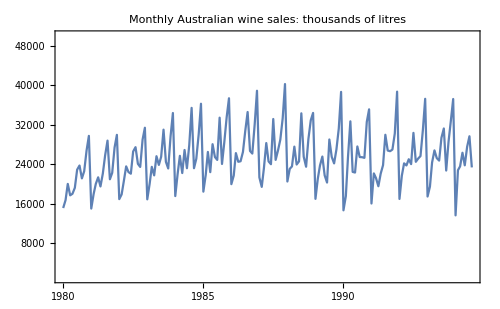

```mathematica
wine=Import["monthly-australian-wine-sales-th.csv"];
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧,PlotLabel->"Monthly Australian wine sales: thousands of litres",ImageSize->500,PlotRange->{All,{1000,50000}}]
```

Заметим, что в декабре продажи вина больше, а в январе продажи падают. Значит, ряд обладает ярко выраженной годовой сезонностью.

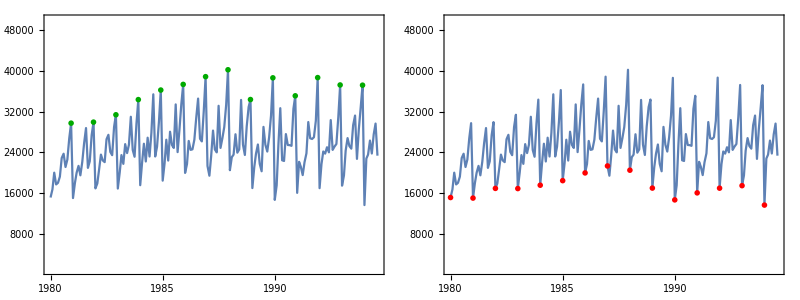

```mathematica
pp={DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧;
Grid[{{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧,PlotRange->{All,{1000,50000}},
Epilog:>{PointSize[0.01],Darker@Green,Point[Select[{DateList[#⟦1⟧],#⟦2⟧}&/@pp,#⟦1⟧⟦2⟧==12&]]},ImageSize->400,AspectRatio->3/4],
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧,PlotRange->{All,{1000,50000}},
Epilog:>{PointSize[0.01],Red,Point[Select[{DateList[#⟦1⟧],#⟦2⟧}&/@pp,#⟦1⟧⟦2⟧==1&]]},ImageSize->400,AspectRatio->3/4]}},Spacings->3]
```

Если построить график зависимости объемов продаж вина в соседние месяцы, то будет видно, что большая часть точек диаграммы рассеяния группируется вокруг главной диагонали. Это говорит о том, что в основном значения продаж в соседние месяцы похожи. Еще одно подмножество точек выделяется в правом нижнем углу, оно связано с падением продаж от декабря к январю, которое было видно на предыдущем графике.

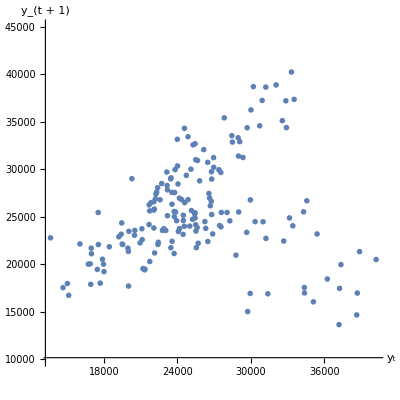

```mathematica
ListPlot[Partition[wine⟦2;;-4,2⟧,2,1],AspectRatio->1,PlotRange->{10000,45000},AxesLabel->{Style[" y_t",14],Style[" y_(t + 1)",14]},ImageSize->400,PlotStyle->PointSize[0.01]]
```

Если построить аналогичный график, но по вертикальной оси отложить y_(t+2), то видно, что точки в основном облаке начинают «расплываться» вокруг главной диагонали, то есть сходство между продажами через месяц уменьшается по сравнению с соседними месяцами. Если посмотреть связь между продажами через два месяца, то облако станет еще шире, а сходство – еще меньше. Однако если рассмотреть продажи в одни и те же месяцы соседних лет, то видно, что точки на графике снова стягиваются к главной диагонали. Это значит, что значения продаж в одни и те же месяцы соседних лет сильно похожи.

```mathematica
Grid[{{Graphics[{{LightBlue,Ellipsoid[{-0.29,0.23},{{11.8,11},{11,16}}]},Point[Partition[Standardize[wine⟦2;;-4,2⟧],2,1]]},Frame->True,AspectRatio->1,PlotLabel->"Соседние месяцы"],
Graphics[{{LightBlue,Ellipsoid[{-0.49,0.3},{{5,4.2},{4.2,12.3}}]},Point[Partition[Standardize[wine⟦2;;-4,2⟧],3,1]⟦All,{1,3}⟧]},Frame->True,AspectRatio->1,PlotLabel->"Через месяц"],
Graphics[{{LightBlue,Ellipsoid[{0,0.02},{{8,0.3},{0.3,7.7}}]},Point[Partition[Standardize[wine⟦2;;-4,2⟧],4,1]⟦All,{1,4}⟧]},Frame->True,AspectRatio->1,PlotLabel->"Через два месяца"],
Graphics[{{LightBlue,Ellipsoid[{0,0},{{13.2,12},{12,13.5}}]},Point[Partition[Standardize[wine⟦2;;-4,2⟧],13,1]⟦All,{1,13}⟧]},Frame->True,AspectRatio->1,PlotLabel->"Через год"]}},
Spacings->2]
```

-Graphics-

### 2.3. Коррелограмма

Анализировать величину автокорреляции при разных значениях лагов удобно с помощью графика, который называется коррелограммой. По оси ординат на нем откладывается автокорреляция, а по оси абсцисс – размер лага τ. На графике для продаж вина в Австралии видно, что автокорреляция принимает большие значения в лагах, кратных сезонному периоду.

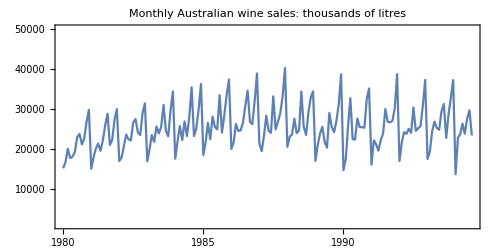

```mathematica
acf[data_,lmax_,clev_:0.95]:=Show[ListPlot[CorrelationFunction[data,{0,lmax}],Filling->Axis,PlotRange->{{0,lmax},All},PlotStyle->PointSize[Medium],AspectRatio->1/2,ImageSize->500],
Graphics[{Dashed,Line[{{0,#},{lmax,#}}]}]&/@(Quantile[NormalDistribution[],{(1-clev)/2,1-(1-clev)/2}]/(√(data["PathLengths"]⟦1⟧)))]
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧,PlotLabel->"Monthly Australian wine sales: thousands of litres",ImageSize->500,AspectRatio->1/2,PlotRange->{All,{1000,50000}}]
```

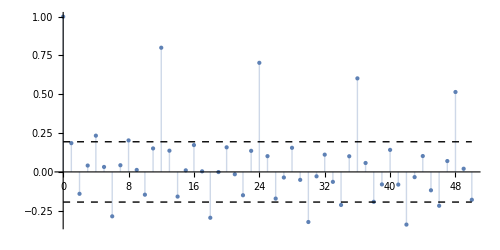

```mathematica
acf[TemporalData[wine⟦2;;-4⟧],50,0.99]
```

### 2.4. Значимость автокорреляции

На первой коррелограмме помимо значений автокорреляции также изображен коридор вокруг горизонтальной оси. Это коридор значимости отличия корреляции от нуля. Как и для обычной корреляции Пирсона, значимость вычисляется с помощью критерия Стьюдента. Альтернатива чаще всего двусторонняя, потому что при анализе временных рядов крайне редко имеется гипотеза о том, какой должна быть корреляция, положительной или отрицательной.

```mathematica
Grid[{{"временной ряд: ","y^T=y_1,...,y_t"},
{"нулевая гипотеза: ","H_0: r_τ=0"},
{"альтернатива: ","H_1: r_τ<≠>0"},
{"статистика: ","T(y^T)=(r_τ √(T-τ-2))/(√(1-r_τ^2))"},
{"нулевое распределение: ","T(y^T)~St(T-τ-2)"}},Frame->All,ItemStyle->{FontFamily->"Georgia",14}]
```

временной ряд:  | y^T=y_1,...,y_t
нулевая гипотеза:  | H_0: r_τ=0
альтернатива:  | H_1: r_τ<≠>0
статистика:  | T(y^T)=(r_τ √(T-τ-2))/(√(1-r_τ^2))
нулевое распределение:  | T(y^T)~St(T-τ-2)

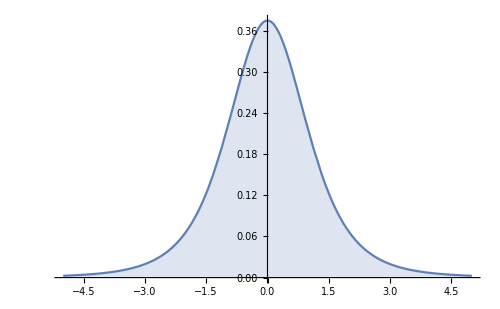

```mathematica
Plot[PDF[StudentTDistribution[4],x]//Evaluate,{x,-5,5},Filling->Axis,ImageSize->500]
```

## 3. Стационарность

### 3.1. Понятие стационарности

Ряд y_1,...,y_T стационарен, если ∀k (ширина окна) распределение y_t,...,y_(t+k) не зависит от t, т.е. его свойства не зависят от времени.

Из этого определения следует, что ряды, в которых присутствует тренд, являются нестационарными: в зависимости от расположения окна изменяется средний уровень ряда. Кроме того, нестационарны ряды с сезонностью: если ширина окна меньше сезонного периода, то распределение ряда будет разным, в зависимости от положения окна. При этом интересно, что ряды, в которых есть непериодические циклы, не обязательно являются нестационарными, поскольку нельзя заранее предсказать положение максимумов и минимумов этого ряда.

#### Упражнение

Какие из представленных ниже рядов являются стационарными?

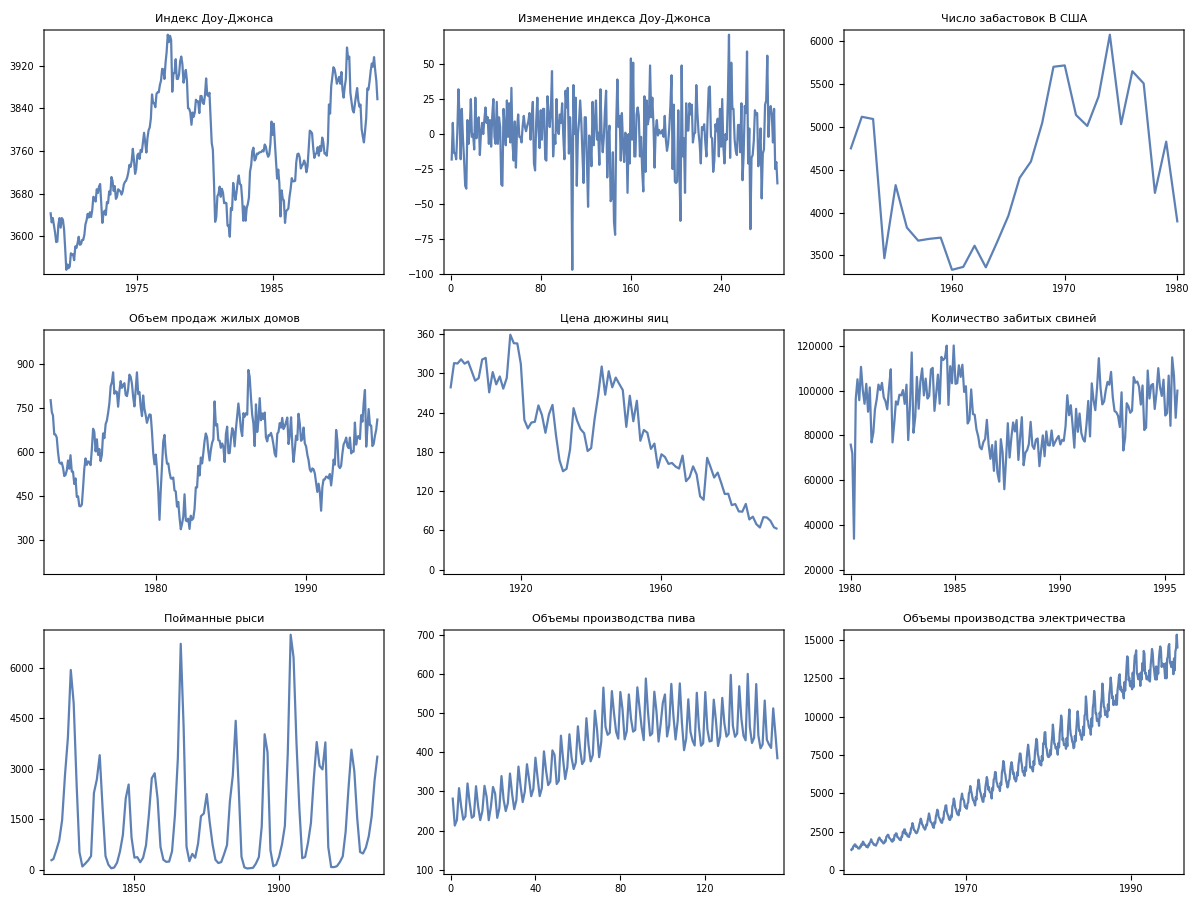

```mathematica
dowjones=Import["monthly-closings-of-the-dowjones.csv"];
strikes=Import["number-of-strikes-in-the-usa-195.csv"];
eggs=Import["price-of-a-dozen-eggs-19001993-i.csv"];
pigs=Import["monthly-total-number-of-pigs-sla.csv"];
lynx=Import["annual-number-of-lynx-trapped-ma.csv"];
beer=Import["quarterly-beer-production-in-aus.csv"];
Grid[{{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@dowjones⟦2;;-4⟧,PlotLabel->"Индекс Доу-Джонса",ImageSize->250,AspectRatio->3/4],
ListLinePlot[Differences@dowjones⟦2;;-4,2⟧,PlotLabel->"Изменение индекса Доу-Джонса",ImageSize->250,AspectRatio->3/4,Frame->True,Axes->False],
DateListPlot[{DateObject[{#⟦1⟧,1}],#⟦2⟧}&/@strikes⟦2;;-4⟧,PlotLabel->"Число забастовок В США",ImageSize->250,AspectRatio->3/4]},
{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@hsales⟦2;;-4⟧,PlotLabel->"Объем продаж жилых домов",ImageSize->250,AspectRatio->3/4,PlotRange->{All,{200,1000}}],
DateListPlot[{DateObject[{#⟦1⟧,1}],#⟦2⟧}&/@eggs⟦2;;-4⟧,PlotLabel->"Цена дюжины яиц",ImageSize->250,AspectRatio->3/4],
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@pigs⟦2;;-4⟧,PlotLabel->"Количество забитых свиней",ImageSize->250,AspectRatio->3/4,PlotRange->{All,{20000,125000}}]},
{DateListPlot[{DateObject[{#⟦1⟧,1}],#⟦2⟧}&/@lynx⟦2;;-4⟧,PlotLabel->"Пойманные рыси",ImageSize->250,AspectRatio->3/4],
ListLinePlot[beer⟦2;;-4,2⟧,PlotLabel->"Объемы производства пива",ImageSize->250,AspectRatio->3/4,Frame->True,Axes->False,PlotRange->{All,{100,700}}],
DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@electricity⟦2;;-4⟧,PlotLabel->"Объемы производства электричества",ImageSize->250,AspectRatio->3/4]
}},Spacings->2]
```

Гипотезу о стационарности можно проверить с помощью критерия Дики-Фуллера. Статистику данного критерия будем рассматривать позже.

### 3.2. Стабилизация дисперсии

Если во временном ряде монотонно по времени изменяется дисперсия, применяется специальное преобразование, стабилизирующее дисперсию. Часто в качестве такого преобразования выступает логарифмирование. В результате логарифмирования ряда производства электричества в Австралии размах колебаний в начале и конце ряда становится очень похожим, и дисперсия примерно стабилизируется.

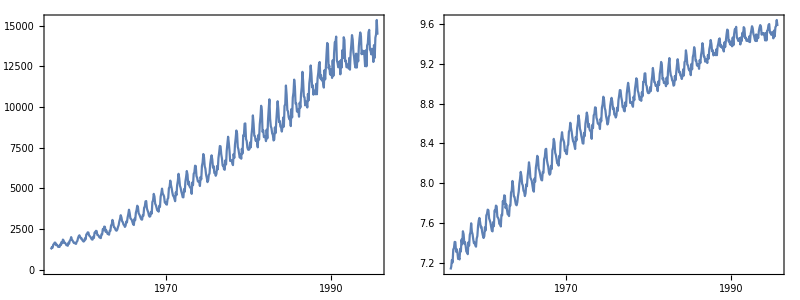

```mathematica
Grid[{{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@electricity⟦2;;-4⟧,ImageSize->400,AspectRatio->3/4],DateListPlot[{DateObject[#⟦1⟧],Log[#⟦2⟧]}&/@electricity⟦2;;-4⟧,ImageSize->390,AspectRatio->3/4]}},Spacings->2]
```

Логарифмирование принадлежит к параметрическому семейству преобразований Бокса-Кокса. В случае, когда значения ряда y>0, преобразование Бокса-Кокса имеет вид:

y^(λ)=Piecewise[{{(y^λ-1)/λ,, λ≠0,}, {log y,, λ=0.}}]

Заметим, что y^λ=ⅇ^(λlog(y))=1+λlog(y)+O((λlog(y))^2). Тогда y^(λ)=log(y) в случае, когда λ бесконечно мало.

Параметр λ определяет, как именно будет преобразован ряд: λ=0 – логарифмирование, λ=1 – тождественное преобразование ряда, при других значениях λ – степенное преобразование. Значение параметра можно подбирать так, чтобы дисперсия была как можно более стабильной во времени. Так, для ряда по данным производства электричества в Австралии оптимальное значение λ=0.27, при этом дисперсия немного более стабильна, чем при логарифмировании.

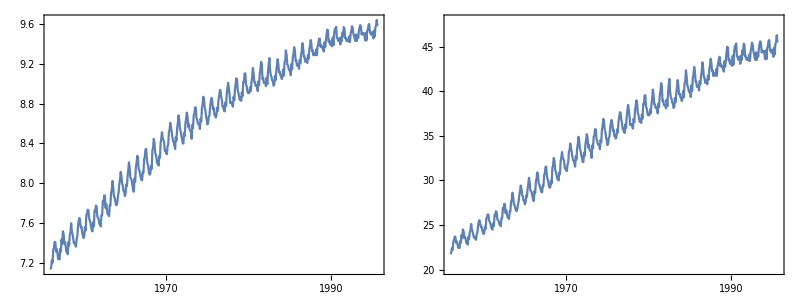

```mathematica
Grid[{{DateListPlot[{DateObject[#⟦1⟧],Log[#⟦2⟧]}&/@electricity⟦2;;-4⟧,ImageSize->400,AspectRatio->3/4],DateListPlot[{DateObject[#⟦1⟧],((#⟦2⟧)^0.27-1)/0.27}&/@electricity⟦2;;-4⟧,ImageSize->390,AspectRatio->3/4,PlotRange->{All,{20,48}}]}},Spacings->2]
```

Параметр λ выбирается методом максимального правдоподобия. Преобразование Бокса-Кокса относится к семейству степенных преобразований вида:

y^(λ)=Piecewise[{{(y^λ-1)/(λ(gm(y)))^(λ-1),, λ≠0,}, {gm(y)log y,, λ=0,}}]

где gm(y)=(∏_(i=1)^T y_i)^(1/T)=(y_1 y_2... y_T)^(1/T) – среднее геометрическое ряда.

Бокс и Кокс в своей статье включили среднее геометрическое в преобразование, связав плотность распределения исходного ряда с плотностью преобразованного следующим соотношением:

J(λ;y_1,y_2,...,y_T)=∏_(i=1)^T |(∂y_i^(λ))/(∂y)|=∏_(i=1)^T y_i^(λ-1)=(gm(y))^(T(λ-1)),
f(y_1,...,y_T)=f_(λ)(y_1^λ,...,y_T^λ)J(λ;y_1,y_2,...,y_T).

Из предположения, что значения ряда y_i^(λ) (i=1,...,T) распределены нормально с математическим ожиданием (ȳ)^(λ) и постоянной дисперсией σ^2, оценка параметра λ может быть получена путем максимизации логарифма правдоподобия:

L_max(λ)=∏_(i=1)^T 1/(√(2π)σ)exp(-((y_i^(λ)-(ȳ)^(λ))^2)/(2 σ^2))J(λ;y),
log(L_max(λ))=-T/2log((∑_i (y_i^(λ)-(ȳ)^(λ))^2)/T)+(λ-1)∑_i log(y_i).

Если ряд содержит отрицательные значения, то можно переписать правила преобразования следующим образом:

y^(λ)=Piecewise[{{((y+λ_2)^λ_1-1)/λ_1,, λ_1≠0,}, {log (y+λ_2),, λ_1=0,}}]

где y>-λ_2.

### 3.3. Дифференцирование

Еще один важный трюк, который позволяет сделать ряд стационарным, – это дифференцирование, переход к попарным разностям соседних значений:

y'_t=y_t-y_(t-1).

Для нестационарного ряда часто оказывается, что получаемый после дифференцирования ряд является стационарным. Такая операция позволяет стабилизировать среднее значение ряда и избавиться от тренда, а иногда даже от сезонности. Кроме того, дифференцирование можно применять неоднократно: от ряда первых разностей, продифференцировав его, можно прийти к ряду вторых разностей, и т. д. Длина ряда при этом каждый раз будет немного сокращаться, но при этом он будет стационарным.

Также может применяться сезонное дифференцирование ряда, переход к попарным разностям значений в соседних сезонах. Если длина периода сезона составляет s, то новый ряд задается разностями:

y'_t=y_t-y_(t-s).

Сезонное и обычное дифференцирование могут применяться к ряду в любом порядке. Однако если у ряда есть ярко выраженный сезонный профиль, то рекомендуется начинать с сезонного дифференцирования, уже после такого преобразования может оказаться, что ряд стационарен.

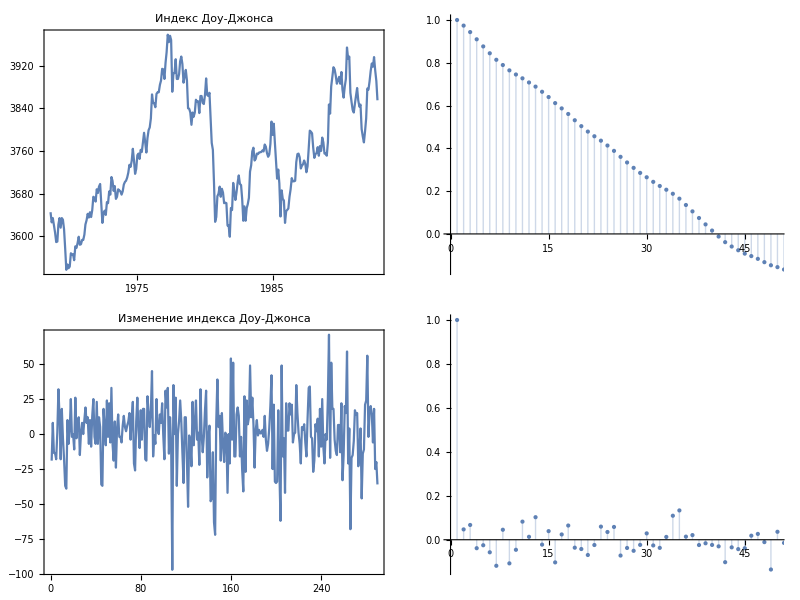

```mathematica
Grid[{{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@dowjones⟦2;;-4⟧,PlotLabel->"Индекс Доу-Джонса",ImageSize->370,AspectRatio->3/4],ListPlot[CorrelationFunction[dowjones⟦2;;-4⟧,{0,50}],Filling->Axis,PlotRange->{{0,50},All},PlotStyle->PointSize[Medium],AspectRatio->3/4,ImageSize->400]},{
ListLinePlot[Differences@dowjones⟦2;;-4,2⟧,PlotLabel->"Изменение индекса Доу-Джонса",ImageSize->370,AspectRatio->3/4,Frame->True,Axes->False],
ListPlot[CorrelationFunction[Differences@dowjones⟦2;;-4,2⟧,{0,50}],Filling->Axis,PlotRange->{{0,50},All},PlotStyle->PointSize[Medium],AspectRatio->3/4,ImageSize->400]}},Spacings->{4,2}]
```

На верхних графиках показаны ряд значений индекса Доу-Джонса и его автокорреляционная функция. Видно, что этот ряд нестационарен – имеется ярко выраженный тренд. От тренда удается полностью избавиться, продифференцировав ряд.

Таким образом, для приведения временного ряда к стационарному первым делом необходимо стабилизировать дисперсию, то есть применить преобразование Бокса-Кокса, затем, при наличии ярко выраженной сезонности провести сезонное дифференцирование с лагом, равным сезонному периоду. При необходимости провести обычное дифференцирование.

### 3.4. Обратное преобразование

Исходя из правил дифференцирования, переход к исходному временному ряду может быть выполнен следующему правилу:

y'_t=y_t-y_(t-k),
y_t=y'_t+y_(t-k),

где y_t – исходный ряд, а k – лаг дифференцирования.